# Riemann Hypothesis

## DirichletSeries

Let Re(s)=σ. For σ>1 the Riemann zeta-function is defined as the Dirichlet series

ζ(s)=∑_(n=1)^∞ 1/n^s.

The Riemann zeta-function had been studied by Euler (Euler 1737) as a function of a real variable. The idea of extending it as a function of a complex variable goes back to Riemann (Riemann 1859).

```mathematica
FullSimplify[∑_(n=1)^∞ 1/n^s,Assumptions->Re[s]>1]
```

Zeta[s]

## EulerProduct

The connection between the zeta function and prime numbers was discovered by Euler (Euler 1737), who proved the following identity. For σ>1 one has

ζ(s)=∏_(p ∈ P) 1/(1-p^-s),

where P={2, 3, 5, 7, 11,...} denotes the set of all primes.

This establishes the connection between the discrete (Euler product) and the continuous (Dirichlet series). The Euler product indicates that the arithmetical properties of integers may be studied with transcendental functions.

This is an analytic version of the fundamental theorem of arithmetic which states that every integer n can be written as a unique product of prime powers, up to the order.

```mathematica
FullSimplify[∏_(k=1)^∞ 1/(1-Prime[k]^-s),Assumptions->Re[s]>1]
```

Zeta[s]

## MellinTransformConnectionGammaFunction

Let Γ(s) := ∫_0^∞ x^(s-1) ⅇ^-x ⅆx be the usual Gamma function. Then for σ>1 one has

Γ(s)ζ(s)=∫_0^∞ x^(s-1)/(ⅇ^x-1)ⅆx.

This establishes that the Mellin transform of ζ(s) is given by the normalized integral above.

This can be proved using geometric summation after a change of variables in the integral.

```mathematica
FullSimplify[∫_0^∞ x^(s-1)/(ⅇ^x-1)ⅆx,Assumptions->Re[s]>1]
```

Gamma[s] Zeta[s]

## FunctionalEquation

The functional equation of ζ(s) provides the stepping stone to establishing its analytic continuation to the whole complex plane ℂ. One has

π^(-s/2)Γ(s/2)ζ(s) =π^(-(1-s)/2)Γ((1-s)/2)ζ(1-s).

Equivalently

ζ(s)=2^s π^(s-1)Sin((π s)/2)Γ(1-s)ζ(1-s).

This is equality of meromorphic functions valid on the whole complex plane. Since the gamma function has no zeros and poles at s=0,-1,-2,-3,... we can deduce that ζ(s) is a meromorphic on ℂ with a simple pole at s=1 with residue equal to 1. Moreover, a consequence of the functional equation is that ζ(s) for s=-2,-4,-6,...

There are several ways to prove this. Titchmarsh (Titchmarsh 1987) presents 8 proofs in Chapter 2 of his book. Riemann (Riemann 1859) presented 2 proofs: one that uses the Poisson summation formula and the functional equation

2 ψ(x)+1=(2 ψ(1/x)+1)/(√x)

of the theta function (x > 0)

ψ(x):=∑_(n=1)^∞ ⅇ^(-n^2 π x).

The other proof requires Cauchy’s residue theorem and the Mellin transform formula.

```mathematica
ψ[x_]:=∑_(n=1)^∞ ⅇ^(-n^2 π x)
```

```mathematica
FullSimplify[2ψ[x]+1-1/(√x)(2ψ[1/x]+1)]
```

-EllipticTheta[3,0,ⅇ^(-π/x)]/(√x)+EllipticTheta[3,0,ⅇ^(-π x)]

```mathematica
difference=Table[2ψ[x]+1-1/(√x)(2ψ[1/x]+1),{x,0.1,10,0.1}];
```

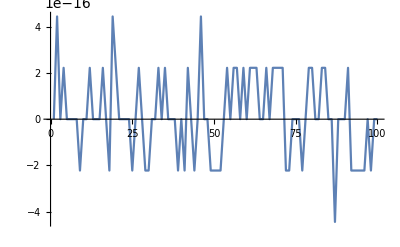

```mathematica
ListLinePlot[difference]
```

```mathematica
FullSimplify[2^s π^(s-1)Sin[(π s)/2]Gamma[1-s]Zeta[1-s]]
```

Zeta[s]

```mathematica
Plot3D[Abs[Zeta[σ + ⅈ t]],{σ,0,1},{t,0,50},ColorFunction->"Rainbow",Filling->Axis]
```

-Graphics3D-

## EarlySpecialValues

From the functional equation we can deduce some early special values (Euler 1737, Titchmarsh 1987).

ζ(1)=+∞,

ζ(0)=-1/2,

For n=1,2, 3,...

ζ(2 n)=((-1)^(n+1) B_(2 n) (2 π)^(2 n))/(2 (2 n)!),

where B_(2 n) are the Bernoulli numbers. In particular ζ(2)=π^2/6. For n=0,1,2, 3,...

ζ(-n)=((-1)^n B_(n+1))/(n+1),

in particular ζ(-1)=-1/12.Finally, we also have

ζ'(0)=-1/2log(2 π),

This shows that ζ(1) is the Harmonic series if we approach from numbers larger than 1, and we now have the first non-trivial values.

This requires manipulations of the Mellin transform formula and the functional equation.

```mathematica
FullSimplify[{Zeta[1],Zeta[0],Zeta'[0]}]
```

{ComplexInfinity,-1/2,-1/2 Log[2 π]}

```mathematica
Table[Zeta[2n],{n,1,5}]
```

{π^2/6,π^4/90,π^6/945,π^8/9450,π^10/93555}

```mathematica
Table[((-1)^(n+1)BernoulliB[2n](2π)^(2n))/(2(2n)!),{n,1,5}]
```

{π^2/6,π^4/90,π^6/945,π^8/9450,π^10/93555}

```mathematica
Table[Zeta[-n],{n,1,5}]
```

{-1/12,0,1/120,0,-1/252}

```mathematica
Table[((-1)^n BernoulliB[n+1])/(n+1),{n,1,5}]
```

{-1/12,0,1/120,0,-1/252}

## XiFunction

It is convenient to define the following function (Riemann 1859).

ξ(s)=1/2 s(s-1)π^-s Γ(s/2)ζ(s) .

This function is entire in ℂ. The non-trivial zeros of ζ(s) are the unique zeros of ξ(s).

```mathematica
Plot3D[Abs[RiemannXi[a+ ⅈ b]],{a,-1,1},{b,-10,10},ColorFunction->"Rainbow",Filling->Axis]
```

-Graphics3D-

## EarlyResultsOnZerosInsideCriticalStripHadamardProduct

The first result on the location of the non-trivial zeros is below (Hadamard 1986).

The function ξ(s) has an infinity of zeros ρ_1,ρ_2,ρ_3,...such that

∑_n |ρ_n|^(-1-ϵ)

converges for any ϵ>0 and ∑|ρ_n|^-1 diverges; and moreover

ξ(s)=ⅇ^(A+B s)∏_ρ (1-s/ρ)ⅇ^(-s/ρ).

The constants A and B are given

A=log(1/2),

and

B=-1/2γ-1+1/2 log(4π),

where γ is the Euler constant. Moreover, ξ(s) has no zeros on the real line so all the zeros are complex. Lastly, let ρ=β+ⅈ γ where γ now denotes the imaginary part of a non-trivial zero (standard notation). Then ρ, 1-ρ,1-ρ̄ are also zeros of ξ(s).

This shows that the are infinitely many zeros inside the critical strip 0≤σ≤1. By the Euler product there are no zeros in the region σ⩾1 and the functional equation there are no zeros in the region σ≤0.

This can be proved on the basis the theory of entire functions of order 1 and Weierstrass’s factorization theorem.

```mathematica
Manipulate[Plot[Abs[Zeta[σ+ ⅈ t]],{t,0,100}],{σ,1/4,3/4}]
```

## AdditionalResultsOnZeros

There is an additional interpretation to the constant B appearing in the Hadamard product. One has that

B=-1/2γ - 1 + 1/2 log(4π) = -∑_ρ 1/ρ = - 2∑_(γ > 0) β/(β^2+γ^2)

This shows that |γ|>6 for all zeros.

This requires manipulating the logarithmic derivative of ξ(s).

```mathematica
N[-∑_(k=1)^1000 (1/ZetaZero[k]+1/(1-ZetaZero[k]))]
```

-0.0223761+0. ⅈ

```mathematica
N[-1/2 EulerGamma-1+1/2 Log[4π]]
```

-0.0230957

## N(T)

Let N(T) denote the number of zeros ρ of ζ(s) inside the rectangle 0<σ<1 and 0<t<T. The formula was stated by Riemann (Riemann 1859) and fully proved by von Mangoldt (von Mangoldt 1905).

N(T)=T/(2π)(log T/(2π)-1)+7/8+S(T)+O(T^-1),

where

S(T)=1/π arg ζ(1/2+ⅈ t)=O(log T).

This provides an efficient way of counting zeros inside the critical strip up to a specified height T.

The main analytic technique behind the proof is the argument principle.

```mathematica
RiemMang[T_]:=T/(2π)(Log[T/(2π)]-1)+7/8
```

```mathematica
N[RiemMang[237]]
```

100.085

```mathematica
N[ZetaZero[100]]
```

0.5+236.524 ⅈ

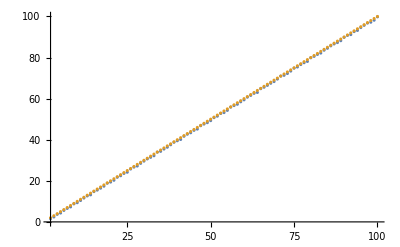

```mathematica
DiscretePlot[{RiemMang[Im[ZetaZero[k]]],k},{k,2,100},Filling->None]
```

```mathematica
difference=Table[Abs[RiemMang[Im[ZetaZero[k]]]-k],{k,4,100}];
```

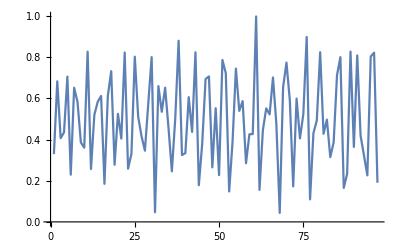

```mathematica
ListLinePlot[difference,Filling->None]
```

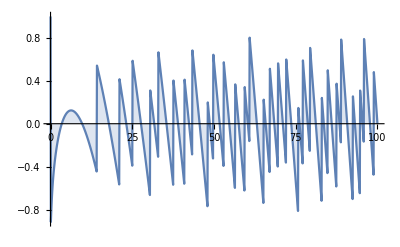

```mathematica
DiscretePlot[Arg[Zeta[1/2+I t]]/Pi,{t,0,100,0.1}]
```

## PrimeNumberTheorem

The knowledge of the location of the zeros has strong arithmetical consequences. The below was proved by Hadamard (Hadamard 1896) and de la Vallée-Poussin (Vallée-Poussin 1896) independently in 1896. It means that there are no zeros on the boundary of the critical strip. One has

ζ(1 + ⅈ t)≠ 0,

for all t∈ ℝ.

Let Li(x):=∫_2^x 1/(log t)ⅆt denote the logarithmic integral and let

π(x):=∑_(p ≤ x
p ∈ P) 1

denote the prime counting function. The arithmetical counterpart of this statement is that π(x)~ Li(x) as x →∞.

The part of the proof involving ζ(1 + ⅈ t)≠ 0 requires a clever use of the inequality 3+4 cos ϕ+cos(2ϕ)=2 (1+(cos ϕ ))^2 ≥0.

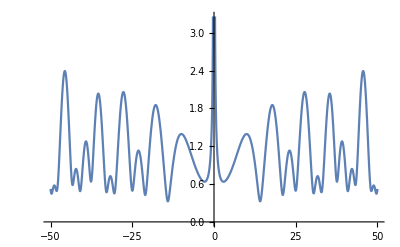

```mathematica
Plot[Abs[Zeta[1+ ⅈ t]],{t,-50,50},AxesOrigin->{0,0}]
```

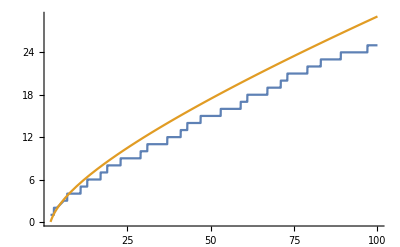

```mathematica
Plot[{PrimePi[x],NIntegrate[1/Log[t],{t,2,x}]},{x,2,100}]
```

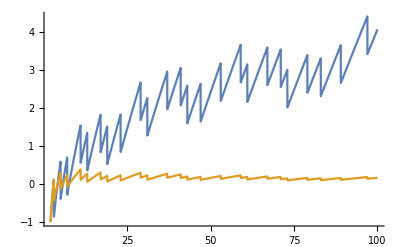

```mathematica
Plot[{-PrimePi[x]+NIntegrate[1/Log[t],{t,2,x}],-(PrimePi[x]-NIntegrate[1/Log[t],{t,2,x}])/PrimePi[x]},{x,2,100}]
```

## ZeroFreeRegion

De la Vallée-Poussin (Vallée-Poussin 1899) was later able to adapt his proof of the prime number theorem to include a rate at for which π(x)~ Li(x), namely π(x)=Li(x)+O(x ⅇ^(-a Log[x])) as x→∞ for some positive constant a. This result is more precise and will have stronger links to the Riemann hypothesis. Let ρ=β+ⅈ t be a generic zero of ζ(s). One has that

1- β ≤ c/(log t).

The above inequality shows that there are no zeros inside the curve defined by that inequality. The weakness is that it is asymptotic to Re(s)=1. This strength of this result has been improved several times but the curve is still asymptotic to Re(s)=1.

This requires manipulations of the Mellin transform formula and the functional equation.

The zero-free region has been enlarged by several authors using methods such as Vinogradov’s mean-value theorem. Ford (Ford, 2002) gave a version with explicit numerical constants. One has that ζ(σ+ⅈ t)≠ 0 whenever|t| ≥ 3 and

σ ≥1- 1/(((57.54 (log |t|))^(2/3)(log log |t|))^(1/3)).

## FirstInstanceRH

Riemann (Riemann 1859) conjectured the following.

All the non-trivial zeros ρ=β+ⅈ γ of ζ(s) are such that β=1/2.

This means that all the complex zeros of ζ(s) are on the critical line and nowhere else. In 1918, Hardy (Hardy 1914) proved that there are infinitely many zeros on the critical line. This is a necessary but not sufficient condition for RH.

## ZerosOnCriticalLine

Let N_0(T) be the number of zeros ρ=1/2+ⅈ t and 0<t<T, i.e. the number of zeros on the critical line up to height T.

Riemann (Riemann 1859) conjectured the following

N_0(T)=N(T)

for all values of T.The best known progress in this direction is due to Selberg (Selberg 1942): there exists a constant 0<c≤1 such that

(N_0(T))/(N(T))→ c.

This means that a finite proportion of the non-trivial zeros of ζ(s) lies on the critical line. In 1974, Levinson (Levinson 1974) showed that c ≥ 0.34, a result later improved by Conrey (Conrey1989) in 1989 to c ≥ 0.4088. The current best bound is c ≥ 0.4149 due to Pratt and Robles (Pratt and Robles, 2017).

## LittlewoodInequality

All numerical evidence points at π(x) < Li(x) and there is no known value of x for which π(x) > Li(x). In 1914, Littlewood proved that there are infinitely many large values of x for which π(x) < Li(x) is false. More precisely

Li(x) - π(x) = Ω_±(x^(1/2)log log log x).

Here Ω_± means that the error achieves the given order of magnitude infinitely often in both positive and negative signs. This result is independent on RH in the sense that first one assumes RH is false and proves it, then one assumes RH is true and proves it. The latter is, oddly, the more difficult case.

Skewes’ (Skewes 1933) number is an estimate on the value of x corresponding to the first sign change. Assuming RH is true, there exists a number x violating π(x) < Li(x) below

ⅇ^(ⅇ^(ⅇ^79))<10^(10^(10^34))

Without assuming RH is true, Skewes (Skewes 1955) showed that there exists a number x violating π(x) < Li(x) below

ⅇ^(ⅇ^(ⅇ^(ⅇ^7.705)))<10^(10^(10^964))

Current best estimates are that there are more than 10^500 consecutive integers x such that π(x) > Li(x) between 1.53×10^1165 and 1.65×10^1165. This is due to (Lehman, 1966). Without assuming RH, te Riele (1987) proved an upper bound of 7×10^370. This was improved to 1.39822×10^316 by Bays and Hudson in 2000. They were also able to show that there are at least 10^153 consecutive integers somewhere near this value such that π(x) > Li(x).

Handle with care! Huge numbers.

```mathematica
N[ⅇ^(ⅇ^(ⅇ^79))]
```

General::ovfl: Overflow occurred in computation.

Indeterminate

## NicolasEulerInequality

In 1963, J. L. Nicolas was able to show that

ϕ(n) < ⅇ^-γ n/(log log n),

for infinitely many values of n. Here ϕ(n) stands for the Euler totient function. This result is independent on RH in the sense that first one assumes RH is false and proves it, then one assumes RH is true and proves it. The latter is, oddly, the more difficult case.

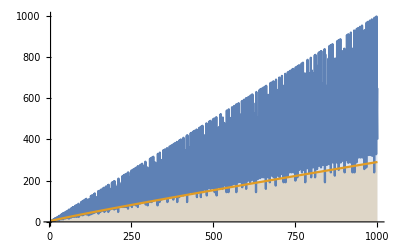

```mathematica
DiscretePlot[{EulerPhi[n],(ⅇ^-EulerGamma n)/Log[Log[n]]},{n,4,1000}]
```

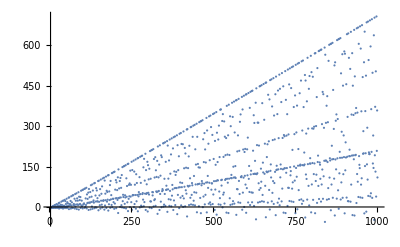

```mathematica
DiscretePlot[{EulerPhi[n]-(ⅇ^-EulerGamma n)/Log[Log[n]]},{n,4,1000},Filling->None]
```

## SelbergMoments

As mentioned in the N(T) section, the number of non-trivial zeros of ζ(s) with imaginary part between 0 and T is given by

N(T) = 1/π arg ξ(s) = 1/π arg (Γ(s/2)π^(-s/2)ζ(s)s(s-1)/2),

where s=σ + ⅈ t and where we take the argument by varying it continuously along the line with Im(s)=T, starting with argument 0 at ∞+ⅈ t. The non-zeta terms yield, thanks to Stirling’s approximation to Γ(s) the contribution

1/π arg (Γ(s/2)π^(-s/2)s(s-1)/2) = T/(2π)log T/(2π)-T/(2π)+7/8+O(1/T),.

The Riemann zeta-function yields

S(T) = 1/π arg ζ(1/2+ⅈ t)  = O(log T).

The function S(t) jumps by 1 at each zero of the zeta function, and for  t≥8, it decreases monotonically between zeros with derivative close to -log t. The interval (T,T+H] for H≥T^(27/82-ϵ) contains at least (H(log T))^(1/3)ⅇ^(-c √(log log T))points where the function S(t) changes sign, see Karatsuba (1996).

The average moments of even powers of S are given by

∫_0^T (Abs(S(t)))^(2k)ⅆt = ((2k)!)/(k!(2π)^(2k))(T(log log T))^k+O((T(log log T))^(k-1/2)),

as shown by Selberg in 1946. This indicates that S(T)/(log log T)^(1/2) mimics a Gaussian random variable with mean 0 and variance 2 π^2, a fact fully proved by Ghosh in 1983. The exact order of S(T) is unknown and there are not unconditional bounds on S(T) beyond the fact that it is O(log T). On the Riemann Hypothesis, one can show that

S(T) ≪ (log T)/(log log T).

It is suspected however, that the true order of magnitude is less than this. This suspicion comes from the observation that random functions with the same distribution as S(T) usually have a growth of order about log^(1/2)T. However, it cannot be too small as Selberg proved that

S(T)= Ω((log^(1/3)T)/(log log T)^(7/3)).

Here Ω denotes the negation of small o. On the other hand, assuming the Riemann hypothesis, Montgomery showed that

S(T)= Ω((log^(1/2)T)/(log log T)^(1/2)).

Numerical evaluations of S show that S(t) grows very slowly: Abs(S(T)) < 1 for T<280 and Abs(S(T)) < 2 for T< 6800000.

```mathematica
S[t_]:=1/π Arg[Zeta[1/2+ⅈ t]]
```

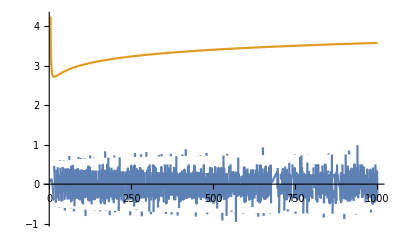

```mathematica
Plot[{S[t],Log[t]/Log[Log[t]]},{t,4,1000}]
```

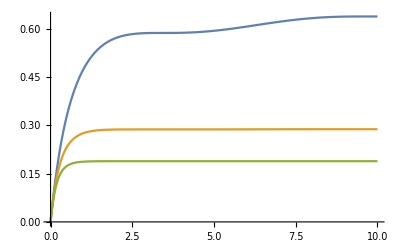

```mathematica
Plot[{NIntegrate[(Abs[S[t]])^2,{t,0,T}],NIntegrate[(Abs[S[t]])^4,{t,0,T}],NIntegrate[(Abs[S[t]])^6,{t,0,T}]},{T,0,10}]
```

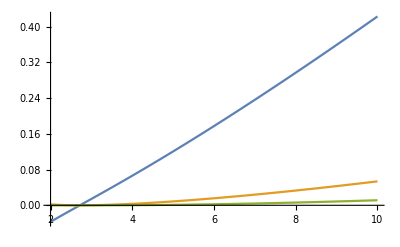

```mathematica
Plot[{((2*1)!)/(1!(2π)^(2*1))T(Log[Log[T]])^1,((2*2)!)/(2!(2π)^(2*2))T(Log[Log[T]])^2,((2*3)!)/(3!(2π)^(2*3))T(Log[Log[T]])^3},{T,2,10}]
```

Riemann’s estimate that S(T)≪log T implies that that the gaps between zeros are bounded. Littlewood improved this by showing that the gaps between their imaginary parts tend to 0.

## ZeroDensityEstimates

Most of non-trivial zeros lie very close to the critical line. Bohr and Landau (1914) showed that for any ϵ>0, all but an infinitely small proportion of zero lie within a distance ϵ of the critical line. These results are called zero-density estimates.

Zero-density estimates involve upper bounds for the function N(σ,T), which represents the number of zeros ρ=β+ⅈσ of the Riemann zeta-function for which β⩾σ⩾0, where σ is fixed and Abs(γ)≤T. Estimates for N(σ,T) are usually written in the form

N(σ, T)≪T^(A(σ)(1-σ))log^C T,

or alternatively

N(σ, T)≪T^(A(σ)(1-σ)+ϵ),

where it is agreed that the symbol ≪ has an implicit constant that is uniform in σ,T and depends only ϵ. The formula for N(T) implies that

A(σ)(1-σ)=1

and C=1 for 0⩽σ⩽1/2, while if σ>1/2, then naturally

A(σ)(1-σ)⩽1.

Also A(σ)(1-σ) is non-increasing. The density hypothesis states that

A(σ)⩽1/2.

for 0⩽σ⩽1/2. The following estimates are known to be true

A(σ)⩽3/(2-σ)   for  (1/2⩽σ⩽3/4)   and  A(σ)⩽3/(3σ-1)   for  (3/4⩽σ⩽1).

A consequence of the first equation is that A(σ)⩽12/5 for 1/2⩽σ⩽1. These estimates are due to Huxley (1972). Estimates in other ranges (depending on the applications) are

A(σ)⩽4/(2σ-1)   for  (17/18⩽σ⩽1)   and  A(σ)⩽24/(30σ-11)   for  (155/174⩽σ⩽17/18).

They are proved in Ivic (1985) by the use of the Halasz-Montgomery inequality. Lastly, let M(α,T)=max_(1⩽ t ⩽T) Abs(ζ(α+ⅈ t)) for 1/2⩽α⩽1. Then for 9/10⩽σ⩽1 one has

N(σ, T)≪ (M(5σ-4, 3T))^(7/6)log^(169/12)T.

This means that if 152/155⩽σ⩽1 then

N(σ, T)≪ T^(1600(1-σ)^(3/2))log^15 T and  N(σ, T)≪ T^(35(1-σ)/36)log^16 T.

This means that if 152/155⩽σ⩽1 then

## HilbertPolyaRandomMatrices

Another way to prove the Riemann hypothesis, as suggested by Hilbert and Polya, would be to find a self-adjoint operator from the existence of which the statement of the real parts of the zeros of ζ(s) would follow when one applies the criterion on the real eigenvalues.

In 1987, Odlyzko showed that the distribution of the zeros of the Riemann zeta-function shares some statistical properties with the eigenvalues of random matrices drawn from the Gaussian unitary ensemble (GUE). This idea gives some numerical evidence to the Hilbert-Polya conjecture.

In 1999, Berry and Keating conjectured that there is some unknown quantization Ĥ of the classical Hamiltonian H=x p so that

ζ(1/2+ ⅈ Ĥ)=0.

In fact, and this is a stronger statement, ρ coincide with the spectrum of the operator 1/2+ ⅈ Ĥ. This quantization is opposed to the the canonical quantization, which leads to the Heisenberg uncertainty principle [x, p] = 1/2 and ℕ as spectrum of the quantum harmonic oscillator. It is of critical importance that Hamiltonian be a self-adjoint operator so that the quantization would be a realization of the Hilbert–Pólya program. Self-adjoint operators have real eigenvalues, implying the Riemann hypothesis.

## BerryConnes

In a connection with this quantum mechanical problem Berry and Connes had proposed that the inverse of the potential of the Hamiltonian is connected to the half-derivative of the function

N(s)=1/π arg ξ(1/2+ⅈ √s).

then in this setting

V^-1(x)=√(4π)ⅆ^(1/2)/(ⅆ x^(1/2))N(x).

This yields a Hamiltonian whose eigenvalues are the square of the imaginary part of the Riemann zeros, and also that the functional determinant of this Hamiltonian operator is just the Riemann Xi function. In fact the Riemann Xi function would be proportional to the functional determinant (Hadamard product)

det(H + 1/4+s(s-1))

as proved by Connes and others, in this approach

(ξ(s))/(ξ(0))=(det(H + 1/4+s(s-1)))/(det(H + 1/4)).

## LindelöfHypothesis

This is a conjecture about the rate of growth of the Riemann zeta function on the critical line that is implied by the Riemann hypothesis. The hypothesis states that for any ϵ>0,

ζ(1/2+ⅈ t) =O(t^ϵ).

as t → ∞. Since ϵ can be replaced by a smaller value, the conjecture can be re-written as: for any ϵ>0,

ζ(1/2+ⅈ t) =o(t^ϵ).

A concept related to the Lindelöf hypothesis is the μ (not to be confused with arithmetical Moebius μ(n) function). In this case, μ is defined to be the infimum of all real numbers a such that ζ(σ+ⅈ T)≪T^a. Clearly μ(σ)=0 for σ>1 and by the functional equation we also have μ(σ)=μ(1-σ)-σ+1/2. By invoking the Phragmen–Lindelöf theorem, we see that μ(σ) is a convex function. The Lindelöf hypothesis states 0, which together with the above properties of μ implies that2.

μ(1/2)=0 for σ≥1/2  
and  
μ(1/2)=1/2−σ for σ≤1/2.

Lindelöf’s convexity result together with μ(1)=0 and μ(0)=1/2 implies that 0≤μ(1/2)≤1/4. This bound was lowered by Hardy and Littlewood to 1/6 by applying Weyl’s method of estimating exponential sums to the approximate functional equation. It has since been lowered to slightly less than 1/6 by several authors using long and technical proofs. The current best bound is due to Bourgain (2017) and it is 13/84.

The Lindelöf hypothesis is related to the Riemann hypothesis as follows. The Lindelöf hypothesis is equivalent to the fact that for every ϵ>0, the number of zeros with real part greater than 1/2+ϵ and imaginary part between T and T+1 is o(log T) as T → ∞ . The Riemann hypothesis is the stronger statement that there are no zeros at all in this region. It is known that the number of zeros with imaginary part between T and T+1 is O(log T) as T → ∞ .

## MontgomeryConjecture

The Montgomery pair correlation conjecture (1973) states that the pair correlation between pairs of zeros of the Riemann zeta function (normalized to have unit average spacing) is

1-((sin (π u))/(π u))^2+δ(u)

where δ(u) is the Dirac delta function.

This means that the chance of finding a zero in a very short interval of length (2π L)/(log T) at a distance (2π u)/(log T) from a zero 1/2+ⅈ T is about L times the expression above. The factor (2π)/(log T) is a normalization factor that can be thought of informally as the average spacing between zeros with imaginary part about T.

The connection with random unitary matrices could lead to a proof of the Riemann hypothesis.

A more precise version is as follows. For a non-trivial zero 1/2+ⅈ γ_n, let the normalized spacings be

δ_n = (γ_(n+1)-γ_n)  1/(2π)log γ_n/(2π).

The conjecture states that

1/M card {(n,k) | N ⩽ n ⩽ N + M, k ⩾ 0, ∑_(i=0)^k δ_(n+i)∈ [α, β]} ~ ∫_α^β (1-((sin (π u))/(π u))^2)ⅆu

as M, N → ∞.

## ToDo

- preliminary information?
- dates, names and references
- categorize
- classify by relationship to RH (equivalences, implications & consequences, proof by cases & independence)
- flow chart